# Estimating temporal dynamics from cross-sectional data using Langevin equations

```mathematica
On[Assert]
Clear["Global`*"]
```

## The code in this subsection deals with importing the file that contains the cross-sectional data and standardizing the data. The file should contain the time-points as columns.

Replace “D:/langevin/data/College_Study_bmis_26_8_2019.csv” with the path of the file which contains the data; if the file is in a format another than CSV, then replace “CSV”  with the file format.

```mathematica
csdata=Import["D:/langevin/data/College_Study_bmis_26_8_2019.csv","CSV"];
```

Separating the header and the data; the first row contains the header and the data is from the second row onwards; the header and data are then used to create the Dataset object.

```mathematica
header=csdata[[1]]; 
data=csdata[[2;;]];
dataset=Thread[header->#]&/@data//Map[Association]//Dataset;
```

Extracting the values from the first column which correspond to the first time-point; these values will be used as the cross-sectional data; replace the column name “BMI_baseline” accordingly. The data is then standardized to have zero median and unit standard deviation.

```mathematica
xdata=Normal[dataset[[All,"BMI_baseline"]]];
xdataStd=(xdata-Median[xdata])/StandardDeviation[xdata];
```

### The code in this subsection deals with the estimation of the probability density function and the free energy landscape from the cross-sectional data and the definition of deterministic term (dF/dx) of the Langevin equation.

Estimating the probability density function (p) from the data using kernel density estimation. Then the estimated probability function (p) is used to estimate the free energy landscape (F). The deterministic term of the Langevin equation is given by dF/dx (diffExpr).

```mathematica
probDist=SmoothKernelDistribution[xdataStd];
p=PDF[probDist,x];
F=-Log[p];
diffExpr=D[-F,x];
```

### The code in this subsection deals with the the determination of the stochastic part of the Langevin equation, i.e., the estimation of the optimal value of σ.

Defining the range of the data through xmin and xmax.

```mathematica
xmin=N[Floor[Min[xdataStd]],1];
xmax=N[Ceiling[Max[xdataStd]],1];
```

statdistMarkov is a function for discretizing the domain of the data, and determining the transition probability matrix (transitionMatrix) and the discrete Markov process (markov). 
Function arguments:
1) the Langevin equation parameters β and σ, 
2) nstds: the number of standard deviations within which the values are considered for the transition probabilities; default value is 4,  and 
3) fineness of the grid; default value is 10. 
The function returns: 
1) xpoints: the discrete points obtained by discretizing the domain of the data,
2) PDF[StationaryDistribution[markov]: the stationary distribution, and
3) Range[numxpoints]]: the range of the number of discrete points (xpoints).

```mathematica
statdistMarkov[β_,σ_,nstds_:4,fineness_:10]:=Block[{dtt=t/.Solve[σ*Sqrt[1000*t]==(xmax-xmin)/2,t][[1]]},
dx=Sqrt[dtt]/fineness;
xpoints=Table[x,{x,xmin,xmax,dx}];
numxpoints=Length[xpoints];

nabla[xt_]:=Evaluate[β(diffExpr/.{x->x[t]})*dtt/.{β->1,x[t]->xt}];
nbrsofi[i_]:=Table[j,{j,Max[1,Floor[Re[i-nstds*σ*Sqrt[dtt]/dx+nabla[xpoints[[i]]]/dx]]],Min[numxpoints,i+Ceiling[Re[nstds*σ*Sqrt[dtt]/dx+nabla[xpoints[[i]]]/dx]]]}];
condLnbrj[j_]:=Block[{nbrsj=nbrsofi[j]},
PDF[NormalDistribution[(xpoints[[i]]+nabla[xpoints[[i]]]),σ*Sqrt[dtt]],xpoints[[nbrsj]]]];

transitionMatrixPositions=Table[Transpose[{Table[i,{Length[nbrsofi[i]]}],nbrsofi[i]}],{i,1,numxpoints}];
transitionMatrixValues=Table[condLnbrj[i],{i,1,numxpoints}];
transitionMatrix=SparseArray[MapThread[#1->#2&,{Flatten[transitionMatrixPositions,1],Flatten[transitionMatrixValues]}],{numxpoints,numxpoints}];
transitionMatrix=transitionMatrix/Map[Total,transitionMatrix];

markov=DiscreteMarkovProcess[Table[1/numxpoints,{numxpoints}],transitionMatrix];
Return[{xpoints,PDF[StationaryDistribution[markov],Range[numxpoints]]}]
]
```

Determining the optimal value of σ using the Hellinger distance (distances) as the cost function. The variable bestsigma gives the optimal σ.

```mathematica
sigmas=Range[0.5,3,0.02];
markovpmfs=Table[statdistMarkov[1,sigma],{sigma,sigmas}]//Parallelize;
markovpdfs=Table[Interpolation[Transpose[pmf]],{pmf,markovpmfs}];
intpdfs=Table[NIntegrate[markovpdf[x1],{x1,xmin,xmax}],{markovpdf,markovpdfs}]//Parallelize;
intdatapdf=NIntegrate[PDF[probDist,x1],{x1,xmin,xmax}];
distances=Table[Re[NIntegrate[(Sqrt[markovpdfs[[ix]][x]/intpdfs[[ix]]]-Sqrt[PDF[probDist,x]/intdatapdf])^2,{x,xmin,xmax},AccuracyGoal->6]],{ix,1,Length[markovpdfs]}]//Parallelize;
bestix=Flatten[Position[distances,Min[distances]]][[1]];
bestsigma=sigmas[[bestix]];
Print[bestsigma];
```

Plot to see how well the model fits the data.

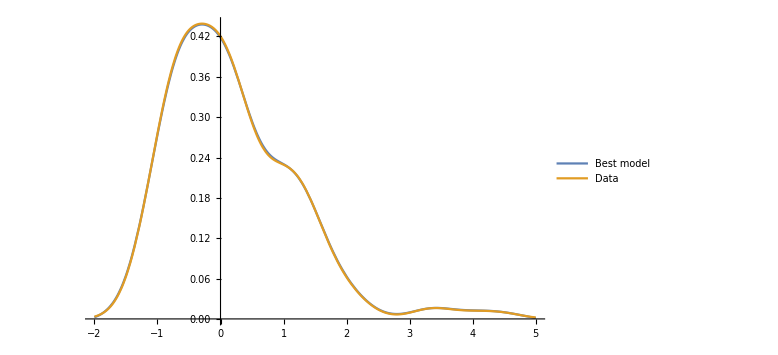

```mathematica
Plot[{markovpdfs[[bestix]][x]/intpdfs[[bestix]],PDF[probDist,x]},{x,xmin,xmax},PlotRange->Automatic,ImageSize->Large,PlotLegends->{"Best model","Data"}]
```

### The code in this subsection deals with defining the complete Langevin stochastic differential equation including both the deterministic and stochastic components, and then generating the timeseries for each of the data-points in the dataset.

Estimate the time series for each data-point in the dataset.
The function MultimodalItoProcess defines the Langevin SDE using the ItoProcess.
Function arguments:
1) the Langevin parameters β and σ. β is set to 1.
2) x0: the initial value of the data-point whose time-series we are estimating.

timeseries gives the integrated SDE. RandomFunction returns a Temporal object, and it takes the integration limit and time step (dt) as arguments. Here we have given the integration limit as 0 to 10^2 and dt as 0.001. Please change these values accordingly.

```mathematica
tempList={}; 
For[indx=1,indx≤Length[xdataStd],indx++,
MultimodalItoProcess[σ_,x0_,β_:1]:=Evaluate[ItoProcess[ⅆx[t]==β(diffExpr/.{x->x[t]})*ⅆt+σ*ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]];
multiproc=MultimodalItoProcess[bestsigma,xdataStd[[indx]]];
dt=0.001;
timeseries=RandomFunction[multiproc,{0,10^2,dt}] ;
timelist=Flatten[timeseries["TimeList"],1]; (*list of time-points from the timeseries*)
valuelist=Flatten[timeseries["ValueList"],1]; (*list of values from the timeseries*)
If[indx==1,AppendTo[tempList,timelist]];
AppendTo[tempList,valuelist];
]
```

Replace “D:/langevin/timeseries.csv” with the path of the file where the timeseries will be saved.

```mathematica
Export["D:/langevin/timeseries.csv",tempList];
```